```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
Lead=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},12,{-0.426777+0. ⅈ,0.+1035.53 ⅈ,0.323223+0. ⅈ,0.-1464.47 ⅈ,-0.176777+0. ⅈ,0.+1035.53 ⅈ,0.0732233+0. ⅈ,0.-1,0.0303301+0. ⅈ,0.+428.932 ⅈ,0.103553+0. ⅈ,0.+428.932 ⅈ,-0.46967+0. ⅈ,0.-1035.53 ⅈ}},299,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
Clear[SR,SL]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
tr[0.7,0.0001,1,0]
```

2.

```mathematica
pris:=pris= Table[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,3,0.01]}]
```

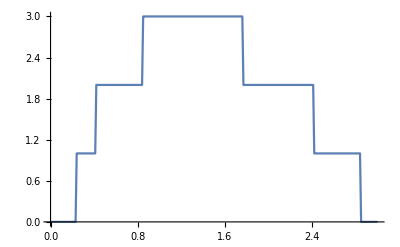

```mathematica
ListLinePlot[pris]
```

```mathematica
misfit2[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},lista={RandomSample[{imp11,imp2,imp,imp5,imp10,imp14,imp7,imp7,imp,imp4,imp,imp,imp,imp,imp14,imp,imp,imp3,imp,imp,imp13,imp,imp8,imp5,imp7,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp,imp,imp,imp3,imp,imp,imp10,imp,imp13,imp12,imp,imp,imp10,imp,imp2,imp,imp,imp,imp8,imp4,imp3,imp,imp,imp4,imp1,imp,imp,imp,imp,imp1,imp9,imp,imp,imp9,imp,imp,imp,imp,imp11,imp,imp9,imp,imp,imp6,imp,imp2,imp,imp11,imp13,imp14,imp,imp5,imp,imp1,imp8,imp,imp,imp,imp12,imp,imp6,imp,imp,imp,imp6}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,3,0.01]}];
υ=Module[{},
ρ0:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/newdata/1imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/newdata/2imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/newdata/3imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/newdata/4imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/newdata/5imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/newdata/6imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/7imp/7imp5.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/8imp/8imp5.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/9imp/9imp5.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/10imp/10imp5.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
Transpose[Join[{Range[1,10,1]},{{ρ1,ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10}}]]];
υ]
```

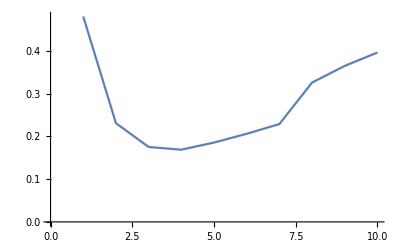

```mathematica
ListLinePlot[misfit2[0.5,1.2,0]]
```

```mathematica
μ1=RandomInteger[{1,14}]; μ2=RandomInteger[{1,14}]; μ3=RandomInteger[{1,14}]; μ4=RandomInteger[{1,14}];μ5=RandomInteger[{1,14}]; μ6=RandomInteger[{1,14}]; μ7=RandomInteger[{1,14}];μ8=RandomInteger[{1,14}]; μ9=RandomInteger[{1,14}]; μ10=RandomInteger[{1,14}]; μ11=RandomInteger[{1,14}];μ12=RandomInteger[{1,14}]; μ13=RandomInteger[{1,14}];   μ14=RandomInteger[{1,14}]
```

1

```mathematica
aa=RandomSample[{imp11,imp2,imp,imp5,imp10,imp14,imp7,imp7,imp,imp4,imp,imp,imp,imp,imp14,imp,imp,imp3,imp,imp,imp13,imp,imp8,imp5,imp7,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp,imp,imp,imp3,imp,imp,imp10,imp,imp13,imp12,imp,imp,imp10,imp,imp2,imp,imp,imp,imp8,imp4,imp3,imp,imp,imp4,imp1,imp,imp,imp,imp,imp1,imp9,imp,imp,imp9,imp,imp,imp,imp,imp11,imp,imp9,imp,imp,imp6,imp,imp2,imp,imp11,imp13,imp14,imp,imp5,imp,imp1,imp8,imp,imp,imp,imp12,imp,imp6,imp,imp,imp,imp6}]
```

{imp14,imp,imp,imp,imp5,imp14,imp,imp,imp11,imp,imp6,imp,imp13,imp3,imp9,imp,imp11,imp13,imp,imp12,imp8,imp,imp,imp,imp4,imp,imp12,imp8,imp7,imp5,imp,imp,imp,imp9,imp,imp1,imp1,imp,imp14,imp,imp10,imp12,imp6,imp10,imp,imp,imp,imp,imp,imp,imp13,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp3,imp,imp,imp9,imp,imp6,imp7,imp,imp,imp,imp,imp,imp,imp,imp,imp11,imp10,imp4,imp,imp4,imp,imp,imp,imp,imp,imp3,imp1,imp2,imp8,imp5,imp,imp,imp7,imp,imp,imp2,imp,imp,imp,imp}

```mathematica
aa=Table[RandomSample[Join[Flatten[Table[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14},3]],Table[imp,58]]],20]
```

{{imp2,imp,imp,imp,imp6,imp8,imp8,imp,imp11,imp,imp,imp,imp,imp,imp10,imp,imp1,imp2,imp12,imp,imp11,imp,imp3,imp,imp,imp,imp,imp9,imp4,imp7,imp,imp,imp13,imp,imp,imp,imp,imp7,imp4,imp12,imp,imp14,imp,imp12,imp13,imp2,imp,imp6,imp,imp,imp,imp,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp1,imp,imp,imp,imp6,imp,imp,imp,imp,imp3,imp8,imp7,imp,imp,imp10,imp,imp,imp,imp,imp5,imp13,imp5,imp,imp10,imp14,imp,imp,imp,imp14,imp,imp9,imp9,imp,imp1,imp3,imp5,imp,imp11,imp},{imp13,imp9,imp12,imp14,imp12,imp,imp,imp4,imp3,imp4,imp,imp,imp5,imp11,imp,imp7,imp7,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp1,imp,imp,imp,imp9,imp8,imp,imp6,imp,imp6,imp,imp4,imp10,imp5,imp3,imp13,imp10,imp14,imp,imp,imp,imp,imp,imp2,imp,imp,imp1,imp8,imp,imp,imp,imp13,imp,imp,imp,imp,imp1,imp11,imp,imp,imp,imp,imp,imp6,imp3,imp,imp,imp,imp,imp12,imp,imp2,imp10,imp,imp,imp14,imp,imp,imp,imp,imp7,imp,imp,imp11,imp,imp,imp2,imp,imp9,imp5,imp,imp,imp8,imp},{imp,imp,imp8,imp,imp7,imp,imp3,imp7,imp6,imp,imp,imp,imp,imp3,imp,imp7,imp,imp,imp,imp,imp3,imp9,imp11,imp,imp1,imp,imp,imp8,imp1,imp,imp,imp,imp,imp11,imp,imp,imp9,imp,imp6,imp,imp10,imp2,imp,imp13,imp,imp2,imp12,imp,imp,imp,imp,imp14,imp,imp4,imp,imp12,imp2,imp14,imp,imp,imp,imp,imp,imp,imp,imp10,imp11,imp,imp,imp4,imp,imp,imp5,imp1,imp8,imp,imp5,imp,imp,imp9,imp13,imp5,imp6,imp14,imp,imp,imp,imp,imp,imp12,imp,imp,imp,imp,imp,imp13,imp10,imp4,imp,imp},{imp14,imp,imp3,imp,imp14,imp,imp12,imp,imp13,imp1,imp,imp14,imp9,imp,imp,imp,imp12,imp,imp8,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp6,imp11,imp,imp2,imp,imp,imp4,imp8,imp2,imp,imp,imp11,imp,imp,imp13,imp6,imp,imp3,imp12,imp,imp,imp,imp10,imp10,imp13,imp9,imp3,imp5,imp,imp,imp,imp6,imp2,imp,imp,imp,imp,imp,imp,imp,imp,imp9,imp4,imp,imp,imp,imp,imp,imp,imp4,imp,imp8,imp10,imp,imp,imp1,imp7,imp5,imp,imp,imp,imp,imp11,imp,imp7,imp,imp7,imp,imp5,imp,imp,imp},{imp,imp12,imp,imp,imp,imp11,imp,imp,imp,imp,imp,imp12,imp13,imp,imp,imp5,imp9,imp2,imp,imp,imp2,imp3,imp,imp,imp4,imp,imp,imp,imp8,imp,imp,imp10,imp,imp4,imp,imp,imp1,imp9,imp,imp5,imp6,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp2,imp14,imp,imp11,imp13,imp,imp,imp,imp14,imp1,imp,imp,imp7,imp,imp9,imp,imp3,imp,imp,imp,imp,imp14,imp,imp,imp,imp13,imp,imp6,imp3,imp,imp6,imp,imp,imp,imp10,imp7,imp8,imp,imp8,imp,imp,imp,imp11,imp12,imp5,imp7,imp,imp1,imp10,imp},{imp3,imp5,imp,imp6,imp,imp,imp,imp1,imp8,imp,imp12,imp7,imp,imp,imp,imp5,imp,imp10,imp11,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp2,imp14,imp13,imp13,imp,imp3,imp9,imp6,imp,imp5,imp,imp,imp4,imp1,imp,imp7,imp,imp11,imp8,imp9,imp8,imp,imp,imp,imp13,imp,imp,imp3,imp,imp,imp,imp,imp10,imp,imp,imp2,imp,imp1,imp12,imp6,imp,imp,imp4,imp,imp14,imp11,imp,imp7,imp,imp,imp14,imp9,imp,imp10,imp,imp,imp4,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp12,imp,imp,imp,imp},{imp3,imp3,imp10,imp,imp,imp9,imp14,imp,imp,imp,imp10,imp,imp,imp1,imp,imp,imp9,imp8,imp13,imp,imp,imp7,imp,imp5,imp,imp3,imp,imp,imp,imp,imp8,imp,imp11,imp,imp6,imp,imp,imp,imp,imp,imp,imp,imp,imp4,imp,imp,imp,imp1,imp10,imp13,imp,imp14,imp,imp12,imp6,imp,imp,imp1,imp11,imp12,imp,imp,imp2,imp,imp4,imp,imp,imp6,imp,imp12,imp11,imp5,imp8,imp5,imp,imp,imp2,imp,imp13,imp,imp,imp7,imp,imp,imp4,imp,imp,imp,imp14,imp,imp2,imp9,imp,imp,imp,imp7,imp,imp,imp,imp},{imp,imp,imp,imp9,imp13,imp4,imp,imp7,imp14,imp,imp3,imp1,imp,imp,imp,imp,imp,imp,imp11,imp10,imp,imp5,imp,imp,imp,imp,imp,imp6,imp12,imp11,imp,imp,imp,imp,imp,imp9,imp13,imp1,imp,imp8,imp9,imp12,imp,imp2,imp,imp13,imp,imp,imp,imp8,imp,imp,imp14,imp,imp8,imp14,imp2,imp12,imp4,imp,imp,imp6,imp,imp7,imp,imp,imp5,imp,imp2,imp10,imp1,imp,imp,imp,imp,imp,imp5,imp,imp,imp6,imp,imp,imp3,imp,imp10,imp,imp,imp11,imp,imp,imp7,imp,imp,imp,imp,imp,imp3,imp,imp4,imp},{imp8,imp,imp,imp,imp,imp7,imp10,imp2,imp9,imp9,imp,imp4,imp,imp5,imp,imp,imp,imp14,imp,imp,imp,imp,imp,imp,imp1,imp,imp,imp13,imp5,imp,imp,imp,imp11,imp,imp7,imp4,imp,imp14,imp,imp5,imp,imp,imp3,imp,imp4,imp,imp,imp,imp,imp,imp,imp9,imp,imp12,imp,imp6,imp,imp,imp14,imp13,imp,imp,imp11,imp10,imp10,imp,imp,imp2,imp6,imp3,imp13,imp,imp,imp,imp,imp6,imp11,imp,imp,imp,imp12,imp,imp,imp,imp2,imp,imp7,imp,imp8,imp12,imp3,imp,imp,imp,imp,imp8,imp1,imp,imp,imp1},{imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp4,imp,imp5,imp,imp6,imp7,imp,imp3,imp7,imp,imp,imp,imp2,imp8,imp9,imp3,imp14,imp,imp,imp,imp12,imp10,imp,imp,imp,imp14,imp,imp,imp10,imp,imp,imp6,imp,imp12,imp13,imp,imp14,imp,imp,imp8,imp,imp3,imp13,imp,imp4,imp,imp1,imp,imp2,imp10,imp,imp11,imp2,imp,imp1,imp11,imp,imp,imp,imp9,imp5,imp,imp8,imp,imp,imp,imp9,imp6,imp,imp,imp,imp7,imp,imp,imp,imp11,imp,imp,imp,imp12,imp,imp1,imp13,imp,imp,imp},{imp,imp,imp4,imp,imp4,imp8,imp,imp,imp,imp,imp12,imp,imp10,imp,imp14,imp,imp,imp,imp,imp9,imp2,imp,imp14,imp,imp11,imp5,imp,imp,imp,imp,imp,imp,imp5,imp,imp10,imp10,imp9,imp,imp6,imp,imp4,imp,imp3,imp11,imp,imp,imp,imp13,imp,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp3,imp2,imp,imp8,imp8,imp13,imp5,imp,imp,imp,imp,imp,imp7,imp12,imp,imp,imp,imp7,imp,imp,imp,imp,imp3,imp11,imp1,imp1,imp6,imp,imp7,imp1,imp,imp13,imp9,imp,imp,imp6,imp,imp12,imp,imp14,imp},{imp3,imp,imp6,imp3,imp14,imp,imp,imp,imp,imp13,imp12,imp,imp8,imp,imp,imp2,imp,imp,imp,imp10,imp,imp,imp,imp7,imp,imp,imp,imp,imp11,imp9,imp7,imp8,imp4,imp,imp,imp1,imp,imp,imp3,imp8,imp,imp,imp,imp11,imp,imp5,imp4,imp,imp14,imp,imp,imp1,imp,imp,imp,imp10,imp14,imp,imp,imp,imp,imp9,imp12,imp,imp,imp5,imp13,imp,imp,imp,imp2,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp12,imp,imp,imp6,imp,imp11,imp,imp1,imp10,imp7,imp9,imp,imp2,imp4,imp,imp5,imp13,imp,imp,imp},{imp,imp,imp,imp7,imp,imp8,imp,imp6,imp,imp,imp,imp,imp,imp11,imp,imp9,imp,imp4,imp,imp6,imp,imp,imp,imp11,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp5,imp14,imp,imp5,imp,imp10,imp10,imp,imp,imp,imp8,imp4,imp,imp,imp,imp8,imp,imp2,imp,imp3,imp,imp,imp13,imp,imp,imp3,imp,imp2,imp,imp13,imp12,imp11,imp,imp,imp14,imp2,imp,imp7,imp,imp,imp4,imp6,imp,imp9,imp,imp,imp12,imp,imp,imp,imp1,imp,imp9,imp13,imp12,imp1,imp,imp10,imp,imp,imp7,imp,imp,imp5,imp14,imp,imp3},{imp8,imp2,imp,imp5,imp,imp,imp,imp6,imp2,imp7,imp,imp,imp4,imp,imp1,imp,imp,imp,imp5,imp,imp,imp,imp,imp,imp6,imp14,imp10,imp11,imp12,imp,imp,imp13,imp,imp8,imp,imp11,imp,imp,imp3,imp13,imp,imp10,imp6,imp13,imp,imp5,imp,imp,imp3,imp8,imp4,imp1,imp,imp,imp,imp,imp,imp11,imp,imp2,imp,imp,imp,imp3,imp,imp,imp,imp9,imp7,imp,imp,imp,imp10,imp,imp,imp14,imp,imp12,imp,imp,imp,imp1,imp,imp,imp,imp9,imp,imp9,imp,imp,imp,imp,imp12,imp,imp14,imp,imp,imp,imp7,imp4},{imp,imp6,imp,imp14,imp10,imp,imp,imp6,imp2,imp13,imp,imp8,imp11,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp,imp,imp12,imp9,imp,imp,imp11,imp,imp5,imp5,imp7,imp9,imp,imp,imp12,imp4,imp4,imp,imp,imp13,imp,imp,imp,imp10,imp,imp1,imp,imp,imp,imp,imp7,imp7,imp,imp9,imp3,imp11,imp1,imp,imp,imp,imp14,imp,imp10,imp,imp,imp8,imp,imp1,imp6,imp,imp2,imp,imp,imp14,imp,imp4,imp,imp,imp,imp,imp12,imp5,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp13,imp3,imp,imp,imp2},{imp6,imp,imp,imp,imp,imp12,imp14,imp,imp13,imp11,imp2,imp10,imp,imp,imp,imp,imp2,imp,imp7,imp3,imp,imp,imp2,imp,imp3,imp,imp1,imp9,imp,imp,imp1,imp10,imp4,imp,imp8,imp,imp7,imp5,imp,imp4,imp,imp,imp,imp,imp,imp,imp12,imp,imp,imp,imp,imp,imp14,imp1,imp,imp,imp,imp,imp,imp13,imp10,imp,imp,imp5,imp,imp,imp,imp8,imp,imp,imp,imp,imp9,imp13,imp7,imp,imp,imp,imp,imp6,imp6,imp8,imp,imp12,imp11,imp5,imp,imp14,imp,imp,imp,imp4,imp,imp3,imp,imp11,imp,imp,imp9,imp},{imp,imp11,imp,imp,imp,imp13,imp,imp4,imp,imp,imp8,imp,imp,imp,imp7,imp1,imp2,imp1,imp6,imp2,imp8,imp4,imp,imp3,imp5,imp,imp,imp,imp,imp13,imp,imp,imp,imp14,imp,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp9,imp,imp12,imp10,imp,imp13,imp,imp,imp14,imp,imp5,imp,imp14,imp,imp11,imp,imp,imp11,imp2,imp,imp12,imp4,imp,imp3,imp,imp,imp,imp,imp10,imp12,imp,imp10,imp,imp,imp,imp5,imp,imp,imp3,imp8,imp,imp6,imp,imp,imp1,imp,imp6,imp,imp,imp7,imp,imp,imp,imp9,imp,imp7},{imp,imp12,imp,imp3,imp,imp,imp,imp14,imp,imp,imp12,imp,imp,imp10,imp3,imp,imp,imp4,imp2,imp13,imp1,imp2,imp,imp,imp,imp10,imp11,imp,imp,imp,imp,imp,imp,imp13,imp,imp,imp,imp,imp2,imp,imp7,imp,imp,imp,imp,imp9,imp,imp,imp,imp,imp7,imp,imp,imp,imp5,imp5,imp4,imp14,imp6,imp8,imp12,imp6,imp1,imp,imp8,imp9,imp,imp,imp,imp,imp9,imp11,imp14,imp7,imp4,imp13,imp3,imp,imp6,imp,imp,imp11,imp,imp,imp10,imp,imp8,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp},{imp9,imp,imp,imp10,imp,imp10,imp,imp,imp,imp,imp7,imp,imp3,imp,imp1,imp,imp,imp,imp13,imp,imp,imp,imp8,imp,imp,imp2,imp,imp,imp,imp,imp12,imp,imp,imp,imp7,imp6,imp7,imp,imp4,imp5,imp,imp,imp13,imp,imp,imp,imp,imp13,imp,imp,imp11,imp,imp14,imp2,imp10,imp,imp,imp,imp,imp5,imp6,imp2,imp5,imp8,imp,imp3,imp4,imp,imp,imp,imp,imp8,imp4,imp,imp,imp9,imp14,imp3,imp,imp1,imp12,imp11,imp,imp,imp1,imp,imp,imp,imp9,imp,imp,imp,imp,imp6,imp12,imp14,imp,imp11,imp,imp},{imp,imp,imp,imp,imp7,imp,imp,imp,imp8,imp8,imp,imp,imp,imp,imp,imp12,imp,imp,imp,imp,imp6,imp10,imp,imp,imp,imp,imp,imp,imp3,imp5,imp4,imp4,imp,imp,imp,imp1,imp,imp12,imp1,imp3,imp5,imp,imp,imp,imp10,imp,imp,imp,imp,imp1,imp,imp9,imp3,imp5,imp6,imp14,imp6,imp13,imp,imp14,imp,imp11,imp,imp2,imp,imp12,imp,imp,imp8,imp2,imp,imp,imp7,imp9,imp11,imp,imp,imp,imp7,imp13,imp,imp,imp,imp10,imp,imp,imp13,imp,imp,imp,imp14,imp,imp,imp,imp11,imp2,imp4,imp,imp9,imp}}

```mathematica
data[n_,ω_,ϵ1_,a_,c_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}],   μ14=RandomInteger[{1,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},lista={{imp2,imp,imp,imp,imp6,imp8,imp8,imp,imp11,imp,imp,imp,imp,imp,imp10,imp,imp1,imp2,imp12,imp,imp11,imp,imp3,imp,imp,imp,imp,imp9,imp4,imp7,imp,imp,imp13,imp,imp,imp,imp,imp7,imp4,imp12,imp,imp14,imp,imp12,imp13,imp2,imp,imp6,imp,imp,imp,imp,imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp1,imp,imp,imp,imp6,imp,imp,imp,imp,imp3,imp8,imp7,imp,imp,imp10,imp,imp,imp,imp,imp5,imp13,imp5,imp,imp10,imp14,imp,imp,imp,imp14,imp,imp9,imp9,imp,imp1,imp3,imp5,imp,imp11,imp},{imp13,imp9,imp12,imp14,imp12,imp,imp,imp4,imp3,imp4,imp,imp,imp5,imp11,imp,imp7,imp7,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp1,imp,imp,imp,imp9,imp8,imp,imp6,imp,imp6,imp,imp4,imp10,imp5,imp3,imp13,imp10,imp14,imp,imp,imp,imp,imp,imp2,imp,imp,imp1,imp8,imp,imp,imp,imp13,imp,imp,imp,imp,imp1,imp11,imp,imp,imp,imp,imp,imp6,imp3,imp,imp,imp,imp,imp12,imp,imp2,imp10,imp,imp,imp14,imp,imp,imp,imp,imp7,imp,imp,imp11,imp,imp,imp2,imp,imp9,imp5,imp,imp,imp8,imp},{imp,imp,imp8,imp,imp7,imp,imp3,imp7,imp6,imp,imp,imp,imp,imp3,imp,imp7,imp,imp,imp,imp,imp3,imp9,imp11,imp,imp1,imp,imp,imp8,imp1,imp,imp,imp,imp,imp11,imp,imp,imp9,imp,imp6,imp,imp10,imp2,imp,imp13,imp,imp2,imp12,imp,imp,imp,imp,imp14,imp,imp4,imp,imp12,imp2,imp14,imp,imp,imp,imp,imp,imp,imp,imp10,imp11,imp,imp,imp4,imp,imp,imp5,imp1,imp8,imp,imp5,imp,imp,imp9,imp13,imp5,imp6,imp14,imp,imp,imp,imp,imp,imp12,imp,imp,imp,imp,imp,imp13,imp10,imp4,imp,imp},{imp14,imp,imp3,imp,imp14,imp,imp12,imp,imp13,imp1,imp,imp14,imp9,imp,imp,imp,imp12,imp,imp8,imp,imp1,imp,imp,imp,imp,imp,imp,imp,imp6,imp11,imp,imp2,imp,imp,imp4,imp8,imp2,imp,imp,imp11,imp,imp,imp13,imp6,imp,imp3,imp12,imp,imp,imp,imp10,imp10,imp13,imp9,imp3,imp5,imp,imp,imp,imp6,imp2,imp,imp,imp,imp,imp,imp,imp,imp,imp9,imp4,imp,imp,imp,imp,imp,imp,imp4,imp,imp8,imp10,imp,imp,imp1,imp7,imp5,imp,imp,imp,imp,imp11,imp,imp7,imp,imp7,imp,imp5,imp,imp,imp},{imp,imp12,imp,imp,imp,imp11,imp,imp,imp,imp,imp,imp12,imp13,imp,imp,imp5,imp9,imp2,imp,imp,imp2,imp3,imp,imp,imp4,imp,imp,imp,imp8,imp,imp,imp10,imp,imp4,imp,imp,imp1,imp9,imp,imp5,imp6,imp4,imp,imp,imp,imp,imp,imp,imp,imp,imp2,imp14,imp,imp11,imp13,imp,imp,imp,imp14,imp1,imp,imp,imp7,imp,imp9,imp,imp3,imp,imp,imp,imp,imp14,imp,imp,imp,imp13,imp,imp6,imp3,imp,imp6,imp,imp,imp,imp10,imp7,imp8,imp,imp8,imp,imp,imp,imp11,imp12,imp5,imp7,imp,imp1,imp10,imp},{imp3,imp5,imp,imp6,imp,imp,imp,imp1,imp8,imp,imp12,imp7,imp,imp,imp,imp5,imp,imp10,imp11,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp2,imp14,imp13,imp13,imp,imp3,imp9,imp6,imp,imp5,imp,imp,imp4,imp1,imp,imp7,imp,imp11,imp8,imp9,imp8,imp,imp,imp,imp13,imp,imp,imp3,imp,imp,imp,imp,imp10,imp,imp,imp2,imp,imp1,imp12,imp6,imp,imp,imp4,imp,imp14,imp11,imp,imp7,imp,imp,imp14,imp9,imp,imp10,imp,imp,imp4,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp12,imp,imp,imp,imp},{imp3,imp3,imp10,imp,imp,imp9,imp14,imp,imp,imp,imp10,imp,imp,imp1,imp,imp,imp9,imp8,imp13,imp,imp,imp7,imp,imp5,imp,imp3,imp,imp,imp,imp,imp8,imp,imp11,imp,imp6,imp,imp,imp,imp,imp,imp,imp,imp,imp4,imp,imp,imp,imp1,imp10,imp13,imp,imp14,imp,imp12,imp6,imp,imp,imp1,imp11,imp12,imp,imp,imp2,imp,imp4,imp,imp,imp6,imp,imp12,imp11,imp5,imp8,imp5,imp,imp,imp2,imp,imp13,imp,imp,imp7,imp,imp,imp4,imp,imp,imp,imp14,imp,imp2,imp9,imp,imp,imp,imp7,imp,imp,imp,imp},{imp,imp,imp,imp9,imp13,imp4,imp,imp7,imp14,imp,imp3,imp1,imp,imp,imp,imp,imp,imp,imp11,imp10,imp,imp5,imp,imp,imp,imp,imp,imp6,imp12,imp11,imp,imp,imp,imp,imp,imp9,imp13,imp1,imp,imp8,imp9,imp12,imp,imp2,imp,imp13,imp,imp,imp,imp8,imp,imp,imp14,imp,imp8,imp14,imp2,imp12,imp4,imp,imp,imp6,imp,imp7,imp,imp,imp5,imp,imp2,imp10,imp1,imp,imp,imp,imp,imp,imp5,imp,imp,imp6,imp,imp,imp3,imp,imp10,imp,imp,imp11,imp,imp,imp7,imp,imp,imp,imp,imp,imp3,imp,imp4,imp},{imp8,imp,imp,imp,imp,imp7,imp10,imp2,imp9,imp9,imp,imp4,imp,imp5,imp,imp,imp,imp14,imp,imp,imp,imp,imp,imp,imp1,imp,imp,imp13,imp5,imp,imp,imp,imp11,imp,imp7,imp4,imp,imp14,imp,imp5,imp,imp,imp3,imp,imp4,imp,imp,imp,imp,imp,imp,imp9,imp,imp12,imp,imp6,imp,imp,imp14,imp13,imp,imp,imp11,imp10,imp10,imp,imp,imp2,imp6,imp3,imp13,imp,imp,imp,imp,imp6,imp11,imp,imp,imp,imp12,imp,imp,imp,imp2,imp,imp7,imp,imp8,imp12,imp3,imp,imp,imp,imp,imp8,imp1,imp,imp,imp1},{imp,imp,imp,imp,imp4,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp4,imp,imp5,imp,imp6,imp7,imp,imp3,imp7,imp,imp,imp,imp2,imp8,imp9,imp3,imp14,imp,imp,imp,imp12,imp10,imp,imp,imp,imp14,imp,imp,imp10,imp,imp,imp6,imp,imp12,imp13,imp,imp14,imp,imp,imp8,imp,imp3,imp13,imp,imp4,imp,imp1,imp,imp2,imp10,imp,imp11,imp2,imp,imp1,imp11,imp,imp,imp,imp9,imp5,imp,imp8,imp,imp,imp,imp9,imp6,imp,imp,imp,imp7,imp,imp,imp,imp11,imp,imp,imp,imp12,imp,imp1,imp13,imp,imp,imp},{imp,imp,imp4,imp,imp4,imp8,imp,imp,imp,imp,imp12,imp,imp10,imp,imp14,imp,imp,imp,imp,imp9,imp2,imp,imp14,imp,imp11,imp5,imp,imp,imp,imp,imp,imp,imp5,imp,imp10,imp10,imp9,imp,imp6,imp,imp4,imp,imp3,imp11,imp,imp,imp,imp13,imp,imp,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp3,imp2,imp,imp8,imp8,imp13,imp5,imp,imp,imp,imp,imp,imp7,imp12,imp,imp,imp,imp7,imp,imp,imp,imp,imp3,imp11,imp1,imp1,imp6,imp,imp7,imp1,imp,imp13,imp9,imp,imp,imp6,imp,imp12,imp,imp14,imp},{imp3,imp,imp6,imp3,imp14,imp,imp,imp,imp,imp13,imp12,imp,imp8,imp,imp,imp2,imp,imp,imp,imp10,imp,imp,imp,imp7,imp,imp,imp,imp,imp11,imp9,imp7,imp8,imp4,imp,imp,imp1,imp,imp,imp3,imp8,imp,imp,imp,imp11,imp,imp5,imp4,imp,imp14,imp,imp,imp1,imp,imp,imp,imp10,imp14,imp,imp,imp,imp,imp9,imp12,imp,imp,imp5,imp13,imp,imp,imp,imp2,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp12,imp,imp,imp6,imp,imp11,imp,imp1,imp10,imp7,imp9,imp,imp2,imp4,imp,imp5,imp13,imp,imp,imp},{imp,imp,imp,imp7,imp,imp8,imp,imp6,imp,imp,imp,imp,imp,imp11,imp,imp9,imp,imp4,imp,imp6,imp,imp,imp,imp11,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp5,imp14,imp,imp5,imp,imp10,imp10,imp,imp,imp,imp8,imp4,imp,imp,imp,imp8,imp,imp2,imp,imp3,imp,imp,imp13,imp,imp,imp3,imp,imp2,imp,imp13,imp12,imp11,imp,imp,imp14,imp2,imp,imp7,imp,imp,imp4,imp6,imp,imp9,imp,imp,imp12,imp,imp,imp,imp1,imp,imp9,imp13,imp12,imp1,imp,imp10,imp,imp,imp7,imp,imp,imp5,imp14,imp,imp3},{imp8,imp2,imp,imp5,imp,imp,imp,imp6,imp2,imp7,imp,imp,imp4,imp,imp1,imp,imp,imp,imp5,imp,imp,imp,imp,imp,imp6,imp14,imp10,imp11,imp12,imp,imp,imp13,imp,imp8,imp,imp11,imp,imp,imp3,imp13,imp,imp10,imp6,imp13,imp,imp5,imp,imp,imp3,imp8,imp4,imp1,imp,imp,imp,imp,imp,imp11,imp,imp2,imp,imp,imp,imp3,imp,imp,imp,imp9,imp7,imp,imp,imp,imp10,imp,imp,imp14,imp,imp12,imp,imp,imp,imp1,imp,imp,imp,imp9,imp,imp9,imp,imp,imp,imp,imp12,imp,imp14,imp,imp,imp,imp7,imp4},{imp,imp6,imp,imp14,imp10,imp,imp,imp6,imp2,imp13,imp,imp8,imp11,imp,imp,imp,imp,imp8,imp,imp,imp,imp,imp,imp,imp12,imp9,imp,imp,imp11,imp,imp5,imp5,imp7,imp9,imp,imp,imp12,imp4,imp4,imp,imp,imp13,imp,imp,imp,imp10,imp,imp1,imp,imp,imp,imp,imp7,imp7,imp,imp9,imp3,imp11,imp1,imp,imp,imp,imp14,imp,imp10,imp,imp,imp8,imp,imp1,imp6,imp,imp2,imp,imp,imp14,imp,imp4,imp,imp,imp,imp,imp12,imp5,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp13,imp3,imp,imp,imp2},{imp6,imp,imp,imp,imp,imp12,imp14,imp,imp13,imp11,imp2,imp10,imp,imp,imp,imp,imp2,imp,imp7,imp3,imp,imp,imp2,imp,imp3,imp,imp1,imp9,imp,imp,imp1,imp10,imp4,imp,imp8,imp,imp7,imp5,imp,imp4,imp,imp,imp,imp,imp,imp,imp12,imp,imp,imp,imp,imp,imp14,imp1,imp,imp,imp,imp,imp,imp13,imp10,imp,imp,imp5,imp,imp,imp,imp8,imp,imp,imp,imp,imp9,imp13,imp7,imp,imp,imp,imp,imp6,imp6,imp8,imp,imp12,imp11,imp5,imp,imp14,imp,imp,imp,imp4,imp,imp3,imp,imp11,imp,imp,imp9,imp},{imp,imp11,imp,imp,imp,imp13,imp,imp4,imp,imp,imp8,imp,imp,imp,imp7,imp1,imp2,imp1,imp6,imp2,imp8,imp4,imp,imp3,imp5,imp,imp,imp,imp,imp13,imp,imp,imp,imp14,imp,imp,imp,imp,imp9,imp,imp,imp,imp,imp,imp9,imp,imp12,imp10,imp,imp13,imp,imp,imp14,imp,imp5,imp,imp14,imp,imp11,imp,imp,imp11,imp2,imp,imp12,imp4,imp,imp3,imp,imp,imp,imp,imp10,imp12,imp,imp10,imp,imp,imp,imp5,imp,imp,imp3,imp8,imp,imp6,imp,imp,imp1,imp,imp6,imp,imp,imp7,imp,imp,imp,imp9,imp,imp7},{imp,imp12,imp,imp3,imp,imp,imp,imp14,imp,imp,imp12,imp,imp,imp10,imp3,imp,imp,imp4,imp2,imp13,imp1,imp2,imp,imp,imp,imp10,imp11,imp,imp,imp,imp,imp,imp,imp13,imp,imp,imp,imp,imp2,imp,imp7,imp,imp,imp,imp,imp9,imp,imp,imp,imp,imp7,imp,imp,imp,imp5,imp5,imp4,imp14,imp6,imp8,imp12,imp6,imp1,imp,imp8,imp9,imp,imp,imp,imp,imp9,imp11,imp14,imp7,imp4,imp13,imp3,imp,imp6,imp,imp,imp11,imp,imp,imp10,imp,imp8,imp1,imp,imp,imp,imp,imp,imp,imp,imp,imp5,imp,imp,imp},{imp9,imp,imp,imp10,imp,imp10,imp,imp,imp,imp,imp7,imp,imp3,imp,imp1,imp,imp,imp,imp13,imp,imp,imp,imp8,imp,imp,imp2,imp,imp,imp,imp,imp12,imp,imp,imp,imp7,imp6,imp7,imp,imp4,imp5,imp,imp,imp13,imp,imp,imp,imp,imp13,imp,imp,imp11,imp,imp14,imp2,imp10,imp,imp,imp,imp,imp5,imp6,imp2,imp5,imp8,imp,imp3,imp4,imp,imp,imp,imp,imp8,imp4,imp,imp,imp9,imp14,imp3,imp,imp1,imp12,imp11,imp,imp,imp1,imp,imp,imp,imp9,imp,imp,imp,imp,imp6,imp12,imp14,imp,imp11,imp,imp},{imp,imp,imp,imp,imp7,imp,imp,imp,imp8,imp8,imp,imp,imp,imp,imp,imp12,imp,imp,imp,imp,imp6,imp10,imp,imp,imp,imp,imp,imp,imp3,imp5,imp4,imp4,imp,imp,imp,imp1,imp,imp12,imp1,imp3,imp5,imp,imp,imp,imp10,imp,imp,imp,imp,imp1,imp,imp9,imp3,imp5,imp6,imp14,imp6,imp13,imp,imp14,imp,imp11,imp,imp2,imp,imp12,imp,imp,imp8,imp2,imp,imp,imp7,imp9,imp11,imp,imp,imp,imp7,imp13,imp,imp,imp,imp10,imp,imp,imp13,imp,imp,imp,imp14,imp,imp,imp,imp11,imp2,imp4,imp,imp9,imp}};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[n,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[n,ζ]],{ζ,a,c}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
Clear[trans]
trans[n_,a_,b_]:= trans[n,a,b]=ParallelTable[{ω,data[n,ω,0.5,a,b]},{ω,Range[0,3,0.01]}]
```

```mathematica
υ100[n_,x_,y_]:=Module[{m5=trans[n,1,100]},
ρ0:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/newdata/1imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/newdata/2imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/newdata/3imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/newdata/4imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/newdata/5imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/newdata/6imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/7imp/7imp5.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/8imp/8imp5.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/9imp/9imp5.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/10imp/10imp5.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
Transpose[Join[{Range[1,10,1]},{{ρ1,ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8,ρ9,ρ10}}]]]
υ10[n_,x_,y_,a_]:=Module[{m5=trans[n,a,a+10]},
ρ0:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/1per.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/2per.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/3per.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/4per.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/5per.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/6per.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/10unitcells/7per.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
Transpose[Join[{Range[1,7,1]},{{ρ1,ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}}]]]
υ20[n_,x_,y_,a_]:=Module[{m5=trans[n,a,a+19]},
ρ0:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/20unitcells/1imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/20unitcells/2imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/20unitcells/3imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/20unitcells/4imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/20unitcells/5imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/20unitcells/6imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/20unitcells/7imp.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
Transpose[Join[{Range[1,7,1]},{{ρ1,ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}}]]]
```

```mathematica
r100[n_]:=υ100[n,1.6,0]
```

```mathematica
r20[n_]:=Table[υ20[n,1.6,0,x],{x,Range[1,90,20]}]
```

```mathematica
r20new[n_]:=Table[υ20[n,1.6,0,x],{x,Range[10,70,20]}]
```

```mathematica
r20[1]
```

{{{1,0.16402},{2,0.0551921},{3,0.0429988},{4,0.0772534},{5,0.114745},{6,0.185699},{7,0.259014}},{{1,0.221107},{2,0.0941911},{3,0.0673844},{4,0.088624},{5,0.1181},{6,0.176275},{7,0.241031}},{{1,0.0731937},{2,0.0290786},{3,0.0637855},{4,0.13455},{5,0.191548},{6,0.286747},{7,0.380472}},{{1,0.116959},{2,0.0421317},{3,0.0588847},{4,0.120552},{5,0.174821},{6,0.267964},{7,0.362073}},{{1,0.324077},{2,0.154401},{3,0.0895755},{4,0.079339},{5,0.0900743},{6,0.125095},{7,0.168965}}}

```mathematica
Table[Position[%64[[x]],Min[%64[[x]]]][[1,1]],{x,5}]
```

{3,3,2,2,4}

```mathematica
υ20[1,1.6,0,80]
```

{{1,0.413771},{2,0.214569},{3,0.1258},{4,0.0960324},{5,0.0965229},{6,0.117754},{7,0.153209}}

```mathematica
r20new[1]
```

{{{1,0.175886},{2,0.0693013},{3,0.0569874},{4,0.0923325},{5,0.12909},{6,0.201283},{7,0.275331}},{{1,0.300736},{2,0.134446},{3,0.07556},{4,0.072885},{5,0.0893224},{6,0.13008},{7,0.180672}},{{1,0.0170354},{2,0.076235},{3,0.19202},{4,0.327069},{5,0.419444},{6,0.560829},{7,0.690889}},{{1,0.229121},{2,0.0859915},{3,0.0470094},{4,0.0598507},{5,0.0848103},{6,0.137026},{7,0.195329}}}

```mathematica
Table[Position[%67[[x]],Min[%67[[x]]]][[1,1]],{x,4}]
```

{3,4,1,3}

```mathematica
r10[n_]:=Join[Table[υ10[n,1.6,0,a],{a,Range[1,90,10]}],{υ10[n,1.6,0,90]}]
```

```mathematica
Table[υ100[n,1.6,0],{n,20}]
```

{{{1,0.454735},{2,0.158703},{3,0.121809},{4,0.161608},{5,0.216376},{6,0.273378},{7,0.322956},{8,0.442644},{9,0.496439},{10,0.542314}},{{1,0.448718},{2,0.164014},{3,0.127651},{4,0.163606},{5,0.218466},{6,0.273604},{7,0.321107},{8,0.43757},{9,0.489385},{10,0.534965}},{{1,0.521575},{2,0.186966},{3,0.125992},{4,0.159496},{5,0.212681},{6,0.269042},{7,0.31617},{8,0.425426},{9,0.477408},{10,0.522205}},{{1,0.492982},{2,0.167097},{3,0.110692},{4,0.140661},{5,0.193179},{6,0.245811},{7,0.290367},{8,0.409003},{9,0.459719},{10,0.503516}},{{1,0.545277},{2,0.18953},{3,0.125467},{4,0.144959},{5,0.187392},{6,0.231123},{7,0.269564},{8,0.357981},{9,0.404366},{10,0.444678}},{{1,0.548233},{2,0.226436},{3,0.172542},{4,0.195241},{5,0.246903},{6,0.300447},{7,0.347685},{8,0.468163},{9,0.516492},{10,0.557767}},{{1,0.470172},{2,0.165628},{3,0.115733},{4,0.14215},{5,0.192304},{6,0.244017},{7,0.289386},{8,0.40942},{9,0.458128},{10,0.500761}},{{1,0.526071},{2,0.181721},{3,0.114586},{4,0.136521},{5,0.183695},{6,0.233463},{7,0.276893},{8,0.383975},{9,0.433216},{10,0.47573}},{{1,0.494994},{2,0.16967},{3,0.119716},{4,0.151454},{5,0.208936},{6,0.262112},{7,0.305288},{8,0.412207},{9,0.463455},{10,0.506891}},{{1,0.534382},{2,0.179452},{3,0.103408},{4,0.115316},{5,0.156492},{6,0.203177},{7,0.245419},{8,0.340591},{9,0.385345},{10,0.424328}},{{1,0.437481},{2,0.143414},{3,0.111356},{4,0.149739},{5,0.208231},{6,0.267278},{7,0.315606},{8,0.436914},{9,0.489067},{10,0.533697}},{{1,0.426481},{2,0.148839},{3,0.121943},{4,0.167684},{5,0.229167},{6,0.290982},{7,0.341678},{8,0.458354},{9,0.512676},{10,0.559268}},{{1,0.504645},{2,0.193963},{3,0.139624},{4,0.167952},{5,0.222203},{6,0.27995},{7,0.32861},{8,0.461521},{9,0.511588},{10,0.555114}},{{1,0.550567},{2,0.20537},{3,0.126832},{4,0.147542},{5,0.193993},{6,0.24654},{7,0.293195},{8,0.419766},{9,0.468755},{10,0.511596}},{{1,0.409287},{2,0.13173},{3,0.10371},{4,0.148883},{5,0.209181},{6,0.268851},{7,0.320182},{8,0.435843},{9,0.489021},{10,0.535817}},{{1,0.455997},{2,0.157135},{3,0.114434},{4,0.146975},{5,0.198504},{6,0.250312},{7,0.293488},{8,0.406077},{9,0.456566},{10,0.498556}},{{1,0.518755},{2,0.196529},{3,0.136521},{4,0.161377},{5,0.21021},{6,0.265211},{7,0.313566},{8,0.429889},{9,0.480142},{10,0.524696}},{{1,0.482848},{2,0.150832},{3,0.0970416},{4,0.130419},{5,0.188477},{6,0.247793},{7,0.298223},{8,0.402507},{9,0.454933},{10,0.499556}},{{1,0.459666},{2,0.138394},{3,0.0846095},{4,0.113345},{5,0.163915},{6,0.215308},{7,0.260429},{8,0.364429},{9,0.414545},{10,0.456533}},{{1,0.54777},{2,0.201945},{3,0.134958},{4,0.157801},{5,0.207833},{6,0.257573},{7,0.300164},{8,0.39822},{9,0.446078},{10,0.488327}}}

```mathematica
Table[Table[Position[r10[n][[x]],Min[r10[n][[x]]]][[1,1]],{x,10}],{n,20}]
```

{{4,4,4,3,4,1,2,4,4,5},{6,3,1,5,4,2,3,3,2,4},{4,2,4,3,4,4,2,4,3,3},{4,4,2,4,4,5,2,3,3,3},{1,4,3,5,2,4,2,3,4,4},{4,4,2,5,5,1,4,5,2,2},{4,4,3,2,3,4,4,4,3,2},{4,3,3,4,4,4,4,2,3,2},{4,2,2,4,1,4,5,3,4,4},{1,3,5,2,3,4,5,3,3,3},{3,4,3,4,3,2,3,2,5,3},{4,3,3,4,3,2,4,2,5,4},{2,3,1,4,3,3,5,4,4,3},{4,2,4,3,5,3,2,2,2,3},{4,2,3,4,2,4,4,3,1,3},{4,4,4,5,1,3,2,3,4,3},{3,5,4,1,3,3,4,3,4,3},{3,5,3,2,2,6,4,5,2,1},{3,3,2,4,2,5,4,5,3,3},{2,2,4,5,2,6,3,4,2,4}}

```mathematica
Table[Join[Table[Abs[10-F[n,x*10]],{x,9}],{10-F[n,90]}],{n,20}]
```

{{3,4,4,5,0,1,3,5,6,6},{4,0,6,5,3,2,4,2,4,4},{1,5,2,4,4,2,5,5,3,3},{4,2,5,4,6,2,3,4,3,3},{4,3,4,2,5,3,3,4,5,5},{4,0,7,6,2,4,4,3,1,1},{4,2,2,3,6,4,6,2,2,2},{3,4,4,5,6,4,3,3,2,2},{3,2,4,2,4,6,3,4,4,4},{4,6,4,4,4,6,3,3,3,3},{3,4,4,3,1,5,2,6,4,4},{4,3,6,4,2,3,1,5,5,5},{3,2,4,3,3,5,4,5,4,4},{3,4,4,6,4,3,2,2,3,3},{3,2,6,2,5,3,4,1,3,3},{5,4,6,1,2,3,3,6,3,3},{6,5,2,3,4,4,3,4,3,3},{5,4,1,1,6,5,7,3,0,0},{3,1,5,2,4,6,5,4,3,3},{1,3,6,3,8,5,5,2,4,4}}

```mathematica
Table[N[Mean[%105[[n]]]],{n,20}]
```

{3.5,3.3,3.3,3.4,3.2,3.4,3.3,3.3,3.3,3.2,3.2,3.4,3.2,3.,3.,3.3,3.3,3.3,3.4,3.4}

```mathematica
N[Mean[{4,4,4,3,4,1,2,4,4,5}]]
```

3.5

```mathematica
F[n_,a_]:=Count[Table[%54[[n]][[x]],{x,Range[a,a+10,1]}],imp]
```